# Problem 3

Mochi and Avocado

For this problem, MAKE SURE to use the Pdelta formula derived in Chapter 5 - Problem 1. 

We’ll derive it again at the end of this document to stress the importance of it.

We’ll be using the constants that Professor Mannasah provides.

```mathematica
Clear["Global`*"]
h = 6.62607004 * 10^-34;
m = 9.10938 * 10^-31;
e = 1.60217 * 10^-19;
ℏ = h/(2*Pi);
nano = 10^-9;

α =Sqrt[(2*m*e)/ℏ^2] *nano;
```

#### The P-Delta matrix and the PP matrix

Yeah, I know, the P-Delta looks like a mess. Seriously though, whatever you have to do, memorize it or memorize how to get it.

PI and PP are on the formula sheet that some people.

```mathematica
Pdelta[λ_] = {{1 + (I*λ*α)/(2*Sqrt[en]) , (I*λ*α)/(2*Sqrt[en])},{-1 *(I*λ*α)/(2*Sqrt[en]) , 1 - (I*λ*α)/(2*Sqrt[en])}};
PP [kx_,l_] = MatrixExp[-I * kx * l * PauliMatrix[3]];
```

#### The Given Information

```mathematica
λ1 = -0.1;
λ2 = -0.2;
λ3 = -0.1;
L = 2;
```

#### The Wave Number

We will only need the wave number of the free particle. That is, all we need is the k when the particle is in free space. The rest is taken care of by P-Delta.

```mathematica
kfp = α*Sqrt[en]; (* wave number of the Free Particle*)
```

#### The Transfer Matrix

All that’s left is the Transfer Matrix now. 

When we plot the M11 (top left of the transfer matrix), the trick is to plot is from the lowest in the case of a potential well or highest for potential barrier lambda value to about 0.

The energies won’t exceed the lowest lambda, or else it is NOT a bound state energy. It also means you probably did the problem wrong, so check that if you have an energy lower than the lowest lambda value.

```mathematica
transferMatrix = Pdelta[λ1].PP[kfp, L].Pdelta[λ2].PP[kfp, L/2].Pdelta[λ3];
```

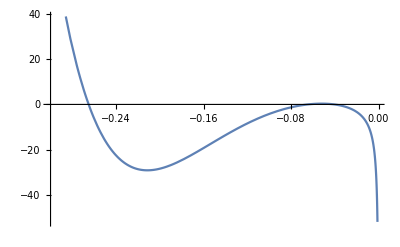

```mathematica
Plot[transferMatrix [[1,1]],{en,-0.3,-0.001}]
```

```mathematica
FindRoot[transferMatrix [[1,1]]==0, {en,-0.26}]
```

{en→-0.265144+0. ⅈ}

# Extra

#### Getting the P-Delta Matrix

Seriously, if you don’t want to memorize it, you have to know how to get it. 

But our suggestion is to MEMORIZE THE ACTUAL P-DELTA.

```mathematica
Clear["Global`*"]
h = 6.62607004 * 10^-34;
m = 9.10938 * 10^-31;
e = 1.60217 * 10^-19;
ℏ = h/(2*Pi);
nano = 10^-9;
α =Sqrt[(2*m*e)/ℏ^2] *nano;
```

#### The PI-PP Matrices

```mathematica
PI[kL_,kR_]= MatrixExp[(1/2) * Log[kL/kR] * ( PauliMatrix[1] - IdentityMatrix[2])];
PP [kx_,l_] = MatrixExp[-I * kx * l * PauliMatrix[3]];
```

#### The wave numbers

```mathematica
V = λ/a;
kδ = α *Sqrt[en- V]; 
k = α *Sqrt[en];
```

#### Getting the P-Delta

```mathematica
pDelta= Limit[PI[k, kδ].PP[kδ, a].PI[kδ,k], a-> 0]
```

{{1.+((0.+2.56158 ⅈ) λ)/(√en),((0.+2.56158 ⅈ) λ)/(√en)},{-((0.+2.56158 ⅈ) λ)/(√en),1.-((0.+2.56158 ⅈ) λ)/(√en)}}

#### Writing it more generally

```mathematica
Pdelta[λ_] = {{1 + (I*λ*α )/(2*Sqrt[en]) , (I*λ*α )/(2*Sqrt[en])},{-1 *(I*λ*α )/(2*Sqrt[en]) , 1 - (I*λ*α )/(2*Sqrt[en])}};
```

#### What is the P-Delta? Why should I use it?

All the transfer matrix is is the transfer matrix through a delta potential. 

Normally, you won’t have to use the P-Delta function. However, since we are using older computers, and using  Mathematica 11 instead of Mathematica 12 on a newer machine, taking the limit to 0 becomes a problem.
If you look at the equation to derive the P-Delta, you’ll see that we are essentially dividing by 0. This is, apparently, very difficult for the computers at school. To give you an idea, if we would have solved this problem on a school computer, it would have taken 2 hours to produce the same answer.
Mathematica 12 also provides more optimized algorithms rather than Mathematica 11. It is NOT fair that the school provides Mathematica 12 for our personal (in-class) use, but provides Mathematica 11 for the exams. Hopefully this problem is corrected before the final exam in Fall 2019, but we are not counting on it.